## Example plot of the Beta variates

AUTHOR: David M. Kipping, Harvard-Smithsonian Center for Astrophysics

Enter the folder path where the inversebetacall.f90 code was executed

```mathematica
thisfolder="/Users/myname/inversebeta/";
```

Execute below code to plot the histogram, which labels the x-axis assuming the distribution is for orbital eccentricities.
Red line is the comparison of the analytic Beta distribution, which the histogram follow (provided you update a & b below, if you changed them in the inversebetacall.f90 code)

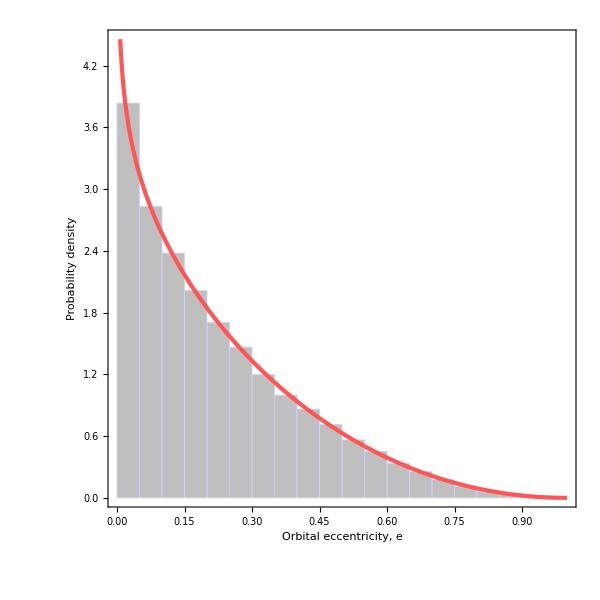

```mathematica
data=Flatten[Import[StringJoin[thisfolder,"beta_variates.dat"],"Table"]];
histogram=Histogram[data,20,"PDF",ChartStyle->Directive[Lighter[Gray],Opacity[0.75]],ImageSize->{600,600},Frame->True,FrameLabel->{"Orbital eccentricity, e","Probability density"},BaseStyle->{"Arial",30},AspectRatio->1,Axes->None,FrameStyle->Directive[Thickness[0.0025],Black]];
a=0.867;
b=3.030;
plots=Show[histogram,Plot[PDF[BetaDistribution[a,b],x],{x,0,1},PlotStyle->{Lighter[Red],Thickness[0.005]}]]
```

Export as a figure

```mathematica
Export[StringJoin[thisfolder,"beta_variates.eps"],plots]
```